## Functions

```mathematica
UncertaintySum[{a_,σa_},X:{_,_}...]:=Fold[{#1[[1]]+#2[[1]],√((#1[[2]])^2+(#2[[2]])^2)}&,{a,σa},{X}]
```

```mathematica
UTPart[m_]:=Diagonal[m,#]&/@Range[Length[m]-1]
```

```mathematica
RealPhotonsPerThrow[data_,atomWindow_,backWindow_]:=Module[{nAtom,nBack,σAtom,σBack,scaleFactor},

nAtom=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,atomWindow]];
nBack=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,backWindow]];

scaleFactor=(Subtract@@atomWindow)/(Subtract@@backWindow);

σAtom=√nAtom;
σBack=√nBack;

{nAtom,σAtom}={nAtom,σAtom}/Length[data];
{nBack,σBack}=scaleFactor{nBack,σBack}/Length[data];

N@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}}

]
```

```mathematica
NCorrelationsPerThrow[data_,detectors_List,idx_List,idxBack_List:Range[101,200]]:=Module[{correls,countsDet1,countsDet2,backCorrels},

{correls,backCorrels}=Transpose[
Table[
Total/@{#[[idx]],#[[idxBack]]}&@SparseArray[Rule@@@Tally[Select[Correlations[data,i,j,4],Positive]],{25000}],{i,detectors},{j,detectors}],
{2,3,1}
];

backCorrels=backCorrels/(Length[idxBack]/Length[idx]);

N@Transpose[{correls-backCorrels,√(correls+backCorrels)}/Length[data],{3,1,2}]
]
```

```mathematica
BulkClean[data1_,countCutOffs_,photonLength_,detectorLagPairs_?MatrixQ]:=Module[{data2},
data2=Select[data1,Between[Length[#],countCutOffs]&];
data2=CompensateDetectorLags[data2,detectorLagPairs,photonLength]
]
```

```mathematica
BulkAnalyse[data2_,{atomWindow_,backWindow_},detectors_]:=Module[{data3,subdividedData,photonMatrix,allCorrelationsMatrix,pm1CorrelationsMatrix},

subdividedData=FilterByPulseParities[#,{EvenQ,OddQ}]&/@FilterByDetector[data2,detectors];

photonMatrix=Map[RealPhotonsPerThrow[#,atomWindow,backWindow]&,subdividedData,{2}];

data3=Function[{m},Select[m,Between[#[[4]],atomWindow]&]]/@data2;

allCorrelationsMatrix=NCorrelationsPerThrow[data3,detectors,Range[100]];
pm1CorrelationsMatrix=NCorrelationsPerThrow[data3,detectors,{1}];

{photonMatrix,allCorrelationsMatrix,pm1CorrelationsMatrix}
]
```

```mathematica
GetPhotonMatrix[bulkAnalysis_]:=bulkAnalysis[[1,;;,;;,1]]

GetPhotonMatrix[bulkAnalysis_,opts_]:=Module[{pm,GetPhotonMatrixOption},
pm=GetPhotonMatrix@bulkAnalysis;

GetPhotonMatrixOption[m_,opt_]:=Switch[opt,
"TotalCounts",
UncertaintySum@@Flatten[m,1],
"TotalCountsByDetector",
UncertaintySum@@@m,
"TotalCountsByParity",
UncertaintySum@@@Transpose@m,
_,
{}
];

If[Length[opts]==0,GetPhotonMatrixOption[pm,opts],GetPhotonMatrixOption[pm,#]&/@opts]
]

GetPhotonMatrixBackground[bulkAnalysis_]:=bulkAnalysis[[1,;;,;;,2]]

GetPhotonMatrixBackground[bulkAnalysis_,opts_]:=Module[{pmb,GetPhotonMatrixOption},
pmb=GetPhotonMatrixBackground@bulkAnalysis;

GetPhotonMatrixOption[m_,opt_]:=Switch[opt,
"TotalCounts",
UncertaintySum@@Flatten[m,1],
"TotalCountsByDetector",
UncertaintySum@@@m,
"TotalCountsByParity",
UncertaintySum@@@Transpose@m,
_,
{}
];

If[Length[opts]==0,GetPhotonMatrixOption[pmb,opts],GetPhotonMatrixOption[pmb,#]&/@opts]
]
```

```mathematica
GetAllCorrelationMatrix[bulkAnalysis_]:=bulkAnalysis[[2]]

GetAllCorrelationMatrix[bulkAnalysis_,opts_]:=Module[{cm,GetCorrelationMatrixOption},
cm=GetAllCorrelationMatrix@bulkAnalysis;

GetCorrelationMatrixOption[m_,opt_]:=Switch[opt,
"CombinedOffDiagonals",
UncertaintySum@@@Flatten[
Riffle[ 
List/@List/@Diagonal[cm],
Transpose/@Transpose[{
UTPart[cm],
UTPart[Transpose@cm]
}]
],
1
],
_,
{}
];

If[Length[opts]==0,GetCorrelationMatrixOption[cm,opts],GetCorrelationMatrixOption[cm,#]&/@opts]
]


GetPM1CorrelationMatrix[bulkAnalysis_]:=bulkAnalysis[[3]]

GetPM1CorrelationMatrix[bulkAnalysis_,opts_]:=Module[{cm,GetCorrelationMatrixOption},
cm=GetPM1CorrelationMatrix@bulkAnalysis;

GetCorrelationMatrixOption[m_,opt_]:=Switch[opt,
"CombinedOffDiagonals",
UncertaintySum@@@Flatten[
Riffle[ 
List/@List/@Diagonal[cm],
Transpose/@Transpose[{
UTPart[cm],
UTPart[Transpose@cm]
}]
],
1
],
_,
{}
];

If[Length[opts]==0,GetCorrelationMatrixOption[cm,opts],GetCorrelationMatrixOption[cm,#]&/@opts]
]
```

## Usage Demo

### (Currently) Static parameters

```mathematica
countCutOffs={0,100};

atomWindow={2.5,14.5}10^3;
backWindow={15,24.5}10^3;

detectors={0,2};
lag[0]=60.*^3;lag[2]=60.*^3;

photonLength=500*^3;

detectorLagPairs=Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}];
```

### Files

```mathematica
date="16-12-09";
files={{"12-43-56","12-38-56"},{"12-38-56"},{"12-33-52"},{"12-28-10"},{"12-23-39"},{"12-18-44"},{"12-13-57"}};
```

### Import and run bulk analysis

```mathematica
data1Raws=ImportDataFiles/@Map[BuildFilePath[root,date,#]&,files,{2}];
```

```mathematica
data2Limiteds=BulkClean[#,countCutOffs,photonLength,detectorLagPairs]&/@data1Raws;
```

```mathematica
AbsoluteTiming[
bulkAnalyses=ParallelMap[BulkAnalyse[#,{atomWindow,backWindow},detectors]&,data2Limiteds];
]
```

{1.08254,Null}

```mathematica
AbsoluteTiming[
bulkAnalyses=ParallelMap[BulkAnalyse[#,{atomWindow,backWindow},detectors]&,data2Limiteds];
]
```

{1.11188,Null}

### Extract desired data from bulk analysis

```mathematica
GetPhotonMatrix[bulkAnalyses[[1]]]
GetPhotonMatrix[bulkAnalyses[[1]],"TotalCounts"]
GetPhotonMatrix[bulkAnalyses[[1]],"TotalCountsByDetector"]
GetPhotonMatrix[bulkAnalyses[[1]],"TotalCountsByParity"]
GetPhotonMatrix[bulkAnalyses[[1]],{"TotalCounts","TotalCountsByDetector"}]
GetPhotonMatrix[bulkAnalyses[[1]],"TotalCountssss"]
```

{{{6.37184,0.184206},{6.37947,0.183921}},{{6.95395,0.196543},{7.16053,0.198254}}}

{26.8658,0.381697}

{{12.7513,0.260305},{14.1145,0.279166}}

{{13.3258,0.269371},{13.54,0.270429}}

{{26.8658,0.381697},{{12.7513,0.260305},{14.1145,0.279166}}}

{}

```mathematica
GetPhotonMatrix[#,"TotalCountsByDetector"]&/@bulkAnalyses
```

{{{12.7513,0.260305},{14.1145,0.279166}},{{14.3132,0.38358},{15.1079,0.408064}},{{13.9208,0.384964},{15.4593,0.41637}},{{13.4258,0.37869},{15.3342,0.407333}},{{10.9769,0.351593},{11.7605,0.369291}},{{12.2952,0.375545},{12.8492,0.38347}},{{14.1621,0.391113},{12.7145,0.373905}}}

```mathematica
GetAllCorrelationMatrix[bulkAnalyses[[1]]]
GetAllCorrelationMatrix[bulkAnalyses[[1]],"CombinedOffDiagonals"]
```

{{{8.405,0.258312},{7.265,0.252636}},{{5.68,0.242899},{6.145,0.254608}}}

{{8.405,0.258312},{12.945,0.350464},{6.145,0.254608}}

### Plotting

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
MakeNice[x_,y_,σy_]:=Transpose[{Transpose[{x,y}],ErrorBar/@σy}]
```

```mathematica
xs=Range[-20.,20,40/6];
```

```mathematica
pdata=Transpose[GetPhotonMatrix[#,"TotalCountsByDetector"]&/@bulkAnalyses]
```

{{{12.7513,0.260305},{14.3132,0.38358},{14.5237,0.617781},{13.4258,0.37869},{11.4014,0.355726},{12.6847,0.379502},{14.7505,0.396516}},{{14.1145,0.279166},{15.1079,0.408064},{15.8753,0.699648},{15.3342,0.407333},{12.2047,0.373649},{13.2385,0.386489},{13.1574,0.377787}},{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}}

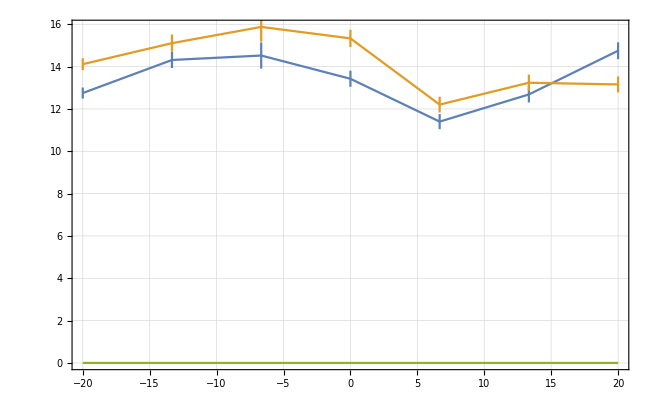

```mathematica
ErrorListPlot[MakeNice[xs,#[[;;,1]],#[[;;,2]]]&/@pdata,
Joined->True,GridLines->Automatic,Frame->True
]
```

## Usage

### (Currently) Static parameters

```mathematica
countCutOffs={1,200};

atomWindow={2.5,9}10^3;
backWindow={17,24.5}10^3;

detectors={0,1};
lag[0]=310.*^3;lag[1]=310.*^3;

photonLength=666*^3;

detectorLagPairs=Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}];
```

### Files

```mathematica
date="17-03-06";
files=List/@{"12-20-13","12-23-13","12-25-11","12-27-08","12-30-04","12-32-07","12-34-29","12-36-19","12-38-26","12-40-25","12-41-56","12-43-59","12-45-29","12-47-00","12-48-25","12-50-21","12-51-38","12-53-15","12-54-28","12-55-47","12-57-07","12-58-31","13-02-30","13-04-15","13-05-33","13-06-46","13-08-23","13-09-41","13-11-00","13-12-35"};
```

### Import and run bulk analysis

```mathematica
data1Raws=ImportDataFiles/@Map[BuildFilePath[root,date,#]&,files,{2}];
```

```mathematica
data2Limiteds=BulkClean[#,countCutOffs,photonLength,detectorLagPairs]&/@data1Raws;
```

```mathematica
AbsoluteTiming[
bulkAnalyses=ParallelMap[BulkAnalyse[#,{atomWindow,backWindow},detectors]&,data2Limiteds];
]
```

{1.20953,Null}

### Plotting

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
MakeNice[x_,y_,σy_]:=Sort@Transpose[{Transpose[{x,y}],ErrorBar/@σy}]
```

```mathematica
xs=Range[Length[files]];
```

```mathematica
pdata=Transpose[GetPhotonMatrix[#,"TotalCountsByDetector"]&/@bulkAnalyses];
```

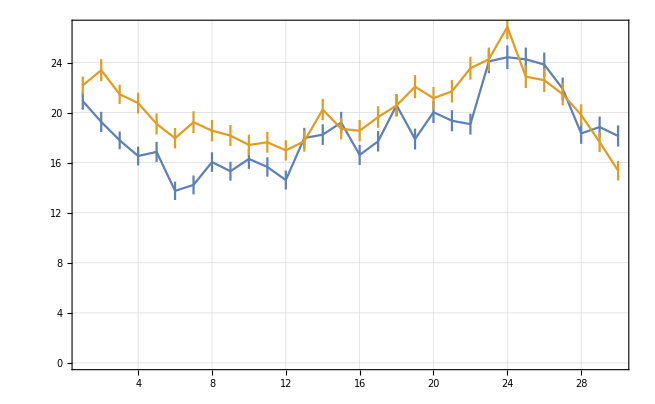

```mathematica
ErrorListPlot[MakeNice[xs,#[[;;,1]],#[[;;,2]]]&/@pdata,
Joined->True,GridLines->Automatic,Frame->True,PlotRange->{All,{0,All}}
]
```

```mathematica
pdata=GetPhotonMatrix[#,"TotalCounts"]&/@bulkAnalyses
```

{{43.092,0.978246},{42.651,1.19322},{39.245,1.04564},{37.2961,1.1203},{35.957,1.15978},{31.7054,1.09445},{33.4575,1.15355},{34.6046,1.15984},{33.4828,1.12694},{33.7149,1.14149},{33.2897,1.13928},{31.5933,1.1071},{35.68,1.16469},{38.4867,1.18841},{37.9103,1.20719},{35.1701,1.17068},{37.3533,1.18385},{41.1655,1.25512},{39.9609,1.24466},{41.18,1.2409},{41.0511,1.22897},{42.6244,1.23494},{48.3556,1.32501},{51.2711,1.35855},{47.1356,1.30131},{46.431,1.3526},{43.3711,1.26857},{38.1489,1.19424},{36.5,1.16253},{33.4943,1.14825}}

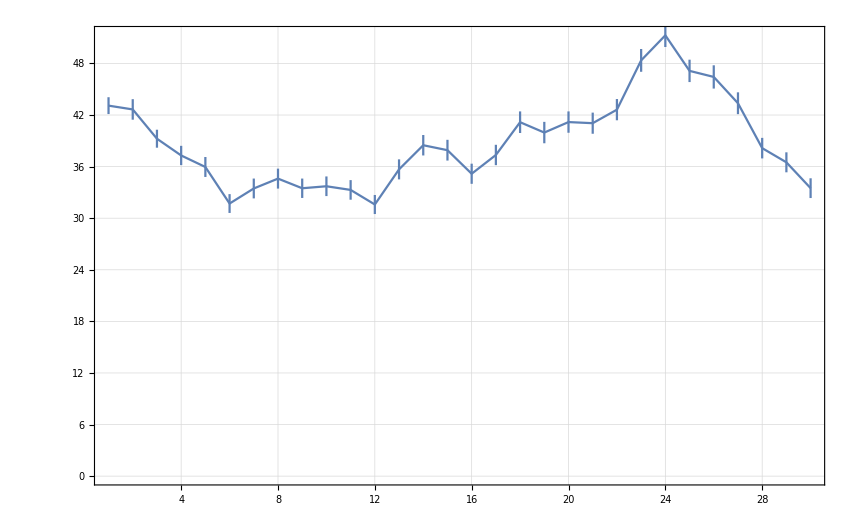

```mathematica
ErrorListPlot[MakeNice[xs,#[[;;,1]],#[[;;,2]]]&@pdata,
Joined->True,GridLines->Automatic,Frame->True,PlotRange->{All,{0,All}}
]
```

```mathematica
pdata1=GetPhotonMatrix[#,"TotalCounts"]&/@bulkAnalyses
pdata2=GetPM1CorrelationMatrix[#,"CombinedOffDiagonals"]&/@bulkAnalyses
```

{{43.092,0.978246},{42.651,1.19322},{39.245,1.04564},{37.2961,1.1203},{35.957,1.15978},{31.7054,1.09445},{33.4575,1.15355},{34.6046,1.15984},{33.4828,1.12694},{33.7149,1.14149},{33.2897,1.13928},{31.5933,1.1071},{35.68,1.16469},{38.4867,1.18841},{37.9103,1.20719},{35.1701,1.17068},{37.3533,1.18385},{41.1655,1.25512},{39.9609,1.24466},{41.18,1.2409},{41.0511,1.22897},{42.6244,1.23494},{48.3556,1.32501},{51.2711,1.35855},{47.1356,1.30131},{46.431,1.3526},{43.3711,1.26857},{38.1489,1.19424},{36.5,1.16253},{33.4943,1.14825}}

{{{2.4624,0.232276},{1.7094,0.210266},{1.9196,0.209781}},{{2.35471,0.275813},{2.15529,0.280138},{2.40118,0.282659}},{{2.25825,0.24707},{2.03725,0.248131},{1.3285,0.198211}},{{1.94353,0.249428},{1.82794,0.256153},{0.870588,0.182258}},{{1.98452,0.263017},{1.62613,0.257237},{1.56484,0.244588}},{{1.36129,0.218309},{1.44806,0.235086},{1.22677,0.213903}},{{1.16172,0.207785},{1.26828,0.231882},{0.762069,0.182139}},{{1.21276,0.214875},{1.0469,0.217104},{0.996552,0.204294}},{{1.31621,0.223021},{1.31828,0.23833},{0.97931,0.199881}},{{2.05828,0.276529},{1.44621,0.248802},{0.872069,0.191092}},{{2.19207,0.28525},{1.53379,0.252267},{1.02172,0.202158}},{{1.62933,0.242945},{1.65967,0.254318},{0.829333,0.185951}},{{1.99333,0.271211},{1.556,0.256732},{0.633667,0.166633}},{{1.63867,0.246847},{1.86967,0.274692},{1.652,0.250422}},{{1.50414,0.239847},{1.33483,0.242093},{0.671724,0.170751}},{{1.16379,0.213264},{1.33483,0.242093},{1.24172,0.223447}},{{2.10367,0.276667},{1.80233,0.270658},{1.044,0.207311}},{{2.45276,0.302329},{2.70448,0.329973},{1.18552,0.227743}},{{2.32483,0.293772},{1.63586,0.272741},{1.53448,0.25222}},{{2.42167,0.300647},{2.19367,0.302196},{1.31067,0.23257}},{{2.269,0.286609},{1.65967,0.262911},{1.64067,0.251175}},{{1.9,0.264575},{1.898,0.28099},{1.53333,0.249444}},{{3.17567,0.341126},{2.375,0.314024},{1.62433,0.252256}},{{2.524,0.309623},{2.88167,0.348887},{1.77967,0.27205}},{{3.77767,0.366166},{2.851,0.340702},{1.70533,0.26}},{{2.94821,0.341534},{2.58107,0.334515},{1.19607,0.227312}},{{2.52333,0.30605},{2.42767,0.311216},{1.753,0.256926}},{{1.41233,0.230048},{1.763,0.268969},{1.566,0.247252}},{{2.35933,0.292916},{2.03633,0.280694},{0.846,0.184451}},{{2.20517,0.288606},{2.16414,0.295105},{0.861379,0.185759}}}

```mathematica
pdata2[[1]]
```

{{2.4624,0.232276},{1.7094,0.210266},{1.9196,0.209781}}

```mathematica
Length@pdata2
```

30